```mathematica
seq=Table[(n^2*Cos[2n])/(8+n^2), {n,1,200}];
seq[[;;;;17]]//TableForm//N
```

-0.0462385
-0.12488
0.62921
-0.944075
0.972016
-0.704789
0.223602
0.3256
-0.776336
0.991997
-0.907211
0.547631

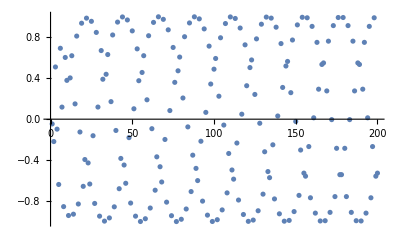

```mathematica
ListPlot[seq,PlotRange->{-1,1}]
```